```mathematica
Clear["Global`*"]
```

```mathematica
num=10; (* Number of terms in Ritz expansion *)
numFreq = 4 ; (* Number of frequencies you want *)
```

```mathematica
h=Table[(x/l)^(i+1),{i,num}];  (* Defining the admissible functions *)
h//MatrixForm;
```

```mathematica
m=Table[0,{i,num},{j,num}]; (* Mass and stiffness matrix *)
k=Table[0,{i,num},{j,num}];
```

```mathematica
For[i=1,i≤num,i++,
For[j=1,j≤num,j++,
m[[i,j]]=Integrate[ρa*h[[i]]*h[[j]],{x,0,l}];
k[[i,j]]=Integrate[ei*D[h[[i]],{x,2}]*D[h[[j]],{x,2}],{x,0,l}]
]
]
```

```mathematica
FullSimplify[m]//MatrixForm;
```

```mathematica
FullSimplify[k]//MatrixForm;
```

```mathematica
ei=(140*10^9*0.05*0.025^3)/12;l=1;ρa=3700*(0.05*0.025); (* Values required for numerical solution *)
```

```mathematica
ω=Sqrt[Eigenvalues[N@{k,m}]]   (* Exact frequencies : 156.0678, 978.2969, 2739.0684, 5367.2073 *)
```

{246282.,48228.7,34354.5,19096.9,13458.2,8873.52,5367.27,2738.91,978.173,156.086}

```mathematica
(*Sort ω values along with their indices*)
sortedOmegaValues=SortBy[Transpose[{ω,Range[Length[ω]]}],First]; 

(*Display sorted ω values with corresponding indices*)
For[i=1,i<=numFreq ,i++,
Print["ω",Subscript[Length[sortedOmegaValues]+1-sortedOmegaValues[[i,2]],""]," = ",sortedOmegaValues[[i,1]]," rad/s"]]
```

ω 1_ = 156.086 rad/s

ω 2_ = 978.173 rad/s

ω 3_ = 2738.91 rad/s

ω 4_ = 5367.27 rad/s

```mathematica
For[i=1,i<=numFreq ,i++,
Print["f",Subscript[Length[sortedOmegaValues]+1-sortedOmegaValues[[i,2]],""]," = ",sortedOmegaValues[[i,1]]/(2*Pi), " Hz"]]
```

f 1_ = 24.8418 Hz

f 2_ = 155.681 Hz

f 3_ = 435.911 Hz

f 4_ = 854.228 Hz

```mathematica
Transpose[Eigensystem[N@{k,m}]]//MatrixForm;
```

```mathematica
v=Eigenvectors[N@{k,m}];
v//MatrixForm
```

(-0.0000440851 | 0.00117275 | -0.0123358 | 0.0689738 | -0.229786 | 0.478984 | -0.630715 | 0.509703 | -0.230769 | 0.0448155
-0.0000795777 | 0.00185914 | -0.0174658 | 0.0883121 | -0.268567 | 0.514735 | -0.626732 | 0.470429 | -0.198535 | 0.0360437
-0.000275355 | 0.00536167 | -0.0415833 | 0.171263 | -0.416283 | 0.6205 | -0.563732 | 0.294914 | -0.0761313 | 0.00596699
0.0000202631 | 0.000347114 | -0.00866971 | 0.0628616 | -0.230732 | 0.492557 | -0.638404 | 0.495874 | -0.212545 | 0.0386908
0.000126385 | 0.000856868 | -0.0235936 | 0.141161 | -0.404098 | 0.640359 | -0.574356 | 0.271494 | -0.0506603 | -0.00129048
-0.00019553 | 0.0011629 | -0.00422874 | 0.0332643 | -0.171003 | 0.449141 | -0.65185 | 0.535217 | -0.233958 | 0.0424476
0.00169198 | -0.00687672 | 0.00976599 | -0.0637306 | 0.304131 | -0.623191 | 0.63577 | -0.325424 | 0.0694539 | -0.00161851
-0.023751 | 0.0619857 | 0.00252838 | -0.0203133 | -0.154547 | -0.00933189 | 0.569458 | -0.717782 | 0.356883 | -0.0658996
0.411557 | -0.655784 | -0.00100343 | 0.00693055 | 0.526955 | -0.307752 | -0.116072 | 0.119498 | -0.0191764 | -0.00250906
0.908433 | -0.416821 | -1.36303×10^-7 | 8.84102×10^-7 | 0.0311921 | -0.0061263 | -0.0000123763 | 0.0000118864 | 0.0000698691 | -7.87071×10^-6)

```mathematica
mode=Table[0,{i,num}];newmode=Table[0,{i,num}];
For[i=num;p=1,i>0,i--;p++,mode[[p]]=∑_(j=1)^num (h[[j]]*v[[i,j]]);newmode[[p]]=mode[[p]]/(mode[[p]]/.x->l)]
Simplify[newmode]//MatrixForm
```

(x^2 (1.75801-0.806636 x-2.63774×10^-7 x^2+1.71092×10^-6 x^3+0.0603633 x^4-0.0118557 x^5-0.0000239507 x^6+0.0000230027 x^7+0.000135211 x^8-0.0000152315 x^9)
x^2 (-11.0172+17.555 x+0.0268613 x^2-0.185528 x^3-14.1063 x^4+8.23838 x^5+3.1072 x^6-3.19891 x^7+0.513344 x^8+0.0671664 x^9)
x^2 (30.8436-80.4959 x-3.28341 x^2+26.3793 x^3+200.699 x^4+12.1186 x^5-739.511 x^6+932.127 x^7-463.456 x^8+85.5787 x^9)
x^2 (-61.2139+248.792 x-353.323 x^2+2305.7 x^3-11003.1 x^4+22546.4 x^5-23001.4 x^6+11773.5 x^7-2512.77 x^8+58.5558 x^9)
x^2 (103.277-614.231 x+2233.57 x^2-17569.8 x^3+90321.8 x^4-237232. x^5+344300. x^6-282696. x^7+123574. x^8-22420.4 x^9)
x^2 (-105.604-715.979 x+19714.2 x^2-117950. x^3+337654. x^4-535069. x^5+479918. x^6-226854. x^7+42330.6 x^8+1078.29 x^9)
x^2 (127.496+2184.06 x-54550.2 x^2+395528. x^3-1.45178×10^6 x^4+3.09919×10^6 x^5-4.01687×10^6 x^6+3.12006×10^6 x^7-1.33734×10^6 x^8+243444. x^9)
x^2 (-699.333+13617.3 x-105611. x^2+434965. x^3-1.05725×10^6 x^4+1.57591×10^6 x^5-1.43174×10^6 x^6+749008. x^7-193354. x^8+15154.7 x^9)
x^2 (893.028-20863.5 x+196003. x^2-991046. x^3+3.01388×10^6 x^4-5.77641×10^6 x^5+7.03325×10^6 x^6-5.2792×10^6 x^7+2.22798×10^6 x^8-404486. x^9)
x^2 (-187.021+4975.14 x-52332. x^2+292607. x^3-974816. x^4+2.03199×10^6 x^5-2.67567×10^6 x^6+2.16231×10^6 x^7-978987. x^8+190120. x^9))

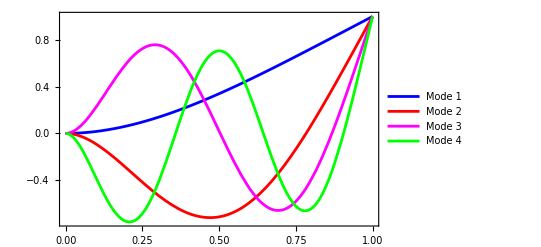

```mathematica
Plot[{newmode[[1]],newmode[[2]],newmode[[3]],newmode[[4]]},{x,0,l},PlotStyle->{{Blue,Thick},{Red,Thick},{Magenta,Thick},{Green,Thick}},Frame->True,PlotLegends->{"Mode 1","Mode 2","Mode 3","Mode 4"}]
```

Wn1_(Normalized)= 1/2 (Sin[(π x)/2]-(-Cos[(π x)/2]+Cosh[(π x)/2]) Sech[π/2] (-1-Sinh[π/2])-Sinh[(π x)/2])

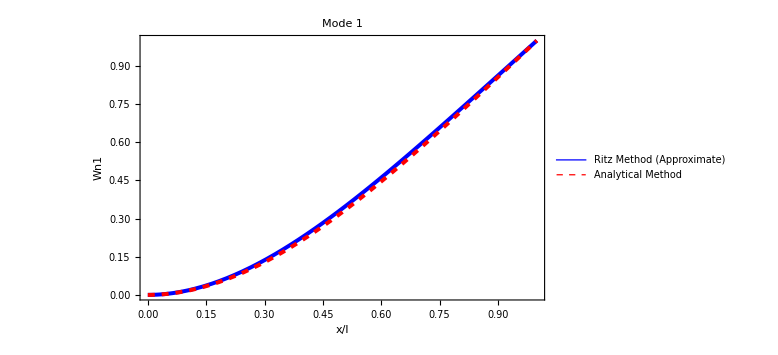

```mathematica
(*Given values*)l=1;
beta[n_]:=-(2*n-1)*Pi/2;

(*Define the expression for Wn(x)*)
Wn[x_,n_]:=Sinh[beta[n]*x]-Sin[beta[n]*x]-((Sinh[beta[n]*l]+Sin[beta[n]*l])/(Cosh[beta[n]*l]+Cos[beta[n]*l]))*(Cosh[beta[n]*x]-Cos[beta[n]*x]);

(*Normalize Wn(x) for n=1*)
maxAbsWn1=MaxValue[{Abs[Wn[x,1]],0<=x<=l},x];
NormalizedWn1[x_]:=Wn[x,1]/maxAbsWn1;
Print["Wn1_(Normalized)= ", NormalizedWn1[x]]

(*Plot*)
Plot[{newmode[[1]],NormalizedWn1[x]},{x,0,l},PlotStyle->{{Blue,Thick,Thickness[0.005]},{Directive[Red,Dashed,Thickness[0.005]]}},Frame->True,FrameLabel->{"x/l","Wn1"},PlotLegends->{"Ritz Method (Approximate)","Analytical Method"},PlotLabel->"Mode 1",ImageSize->Large]
```

Wn2_(Normalized)= 1/2 (-Sin[(3 π x)/2]-(-Cos[(3 π x)/2]+Cosh[(3 π x)/2]) Sech[(3 π)/2] (-1+Sinh[(3 π)/2])+Sinh[(3 π x)/2])

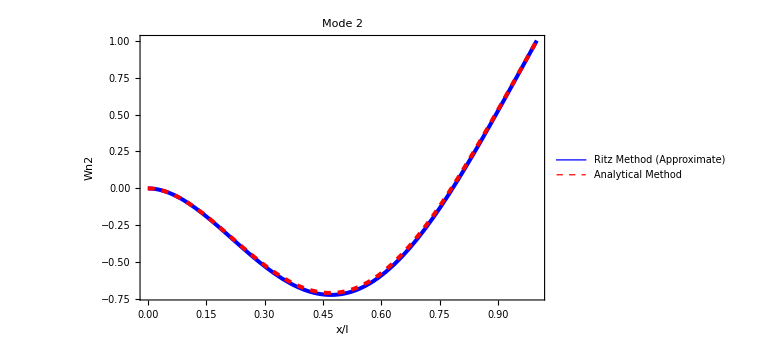

```mathematica
(*Given values*)l=1;
beta[n_]:=(2*n-1)*Pi/2;

(*Define the expression for Wn(x)*)
Wn[x_,n_]:=Sinh[beta[n]*x]-Sin[beta[n]*x]-((Sinh[beta[n]*l]+Sin[beta[n]*l])/(Cosh[beta[n]*l]+Cos[beta[n]*l]))*(Cosh[beta[n]*x]-Cos[beta[n]*x]);

(*Normalize Wn(x) for n=2*)
maxAbsWn2=MaxValue[{Abs[Wn[x,2]],0<=x<=l},x];
NormalizedWn2[x_]:=Wn[x,2]/maxAbsWn2;
Print["Wn2_(Normalized)= ", NormalizedWn2[x]]

(*Plot*)
Plot[{newmode[[2]],NormalizedWn2[x]},{x,0,l},PlotStyle->{{Blue,Thick,Thickness[0.005]},{Directive[Red,Dashed,Thickness[0.005]]}},Frame->True,FrameLabel->{"x/l","Wn2"},PlotLegends->{"Ritz Method (Approximate)","Analytical Method"},PlotLabel->"Mode 2",ImageSize->Large]
```

Wn3_(Normalized)= 1/2 (Sin[(5 π x)/2]-(-Cos[(5 π x)/2]+Cosh[(5 π x)/2]) Sech[(5 π)/2] (-1-Sinh[(5 π)/2])-Sinh[(5 π x)/2])

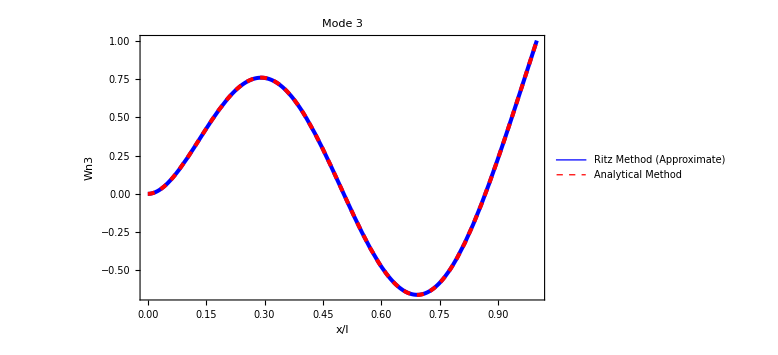

```mathematica
(*Given values*)l=1;
beta[n_]:=-(2*n-1)*Pi/2;

(*Define the expression for Wn(x)*)
Wn[x_,n_]:=Sinh[beta[n]*x]-Sin[beta[n]*x]-((Sinh[beta[n]*l]+Sin[beta[n]*l])/(Cosh[beta[n]*l]+Cos[beta[n]*l]))*(Cosh[beta[n]*x]-Cos[beta[n]*x]);

(*Normalize Wn(x) for n=3*)
maxAbsWn3=MaxValue[{Abs[Wn[x,3]],0<=x<=l},x];
NormalizedWn3[x_]:=Wn[x,3]/maxAbsWn3;
Print["Wn3_(Normalized)= ", NormalizedWn3[x]]

(*Plot*)
Plot[{newmode[[3]],NormalizedWn3[x]},{x,0,l},PlotStyle->{{Blue,Thick,Thickness[0.005]},{Directive[Red,Dashed,Thickness[0.005]]}},Frame->True,FrameLabel->{"x/l","Wn3"},PlotLegends->{"Ritz Method (Approximate)","Analytical Method"},PlotLabel->"Mode 3",ImageSize->Large]
```

Wn4_(Normalized)= 1/2 (-Sin[(7 π x)/2]-(-Cos[(7 π x)/2]+Cosh[(7 π x)/2]) Sech[(7 π)/2] (-1+Sinh[(7 π)/2])+Sinh[(7 π x)/2])

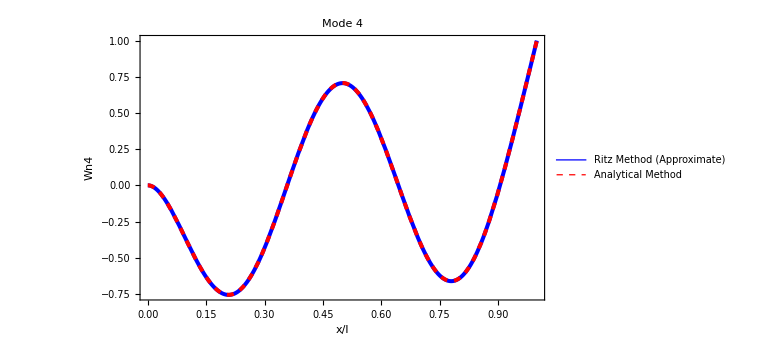

```mathematica
(*Given values*)l=1;
beta[n_]:=(2*n-1)*Pi/2;

(*Define the expression for Wn(x)*)
Wn[x_,n_]:=Sinh[beta[n]*x]-Sin[beta[n]*x]-((Sinh[beta[n]*l]+Sin[beta[n]*l])/(Cosh[beta[n]*l]+Cos[beta[n]*l]))*(Cosh[beta[n]*x]-Cos[beta[n]*x]);

(*Normalize Wn(x) for n=4*)
maxAbsWn4=MaxValue[{Abs[Wn[x,4]],0<=x<=l},x];
NormalizedWn4[x_]:=Wn[x,4]/maxAbsWn4;
Print["Wn4_(Normalized)= ", NormalizedWn4[x]]

(*Plot*)
Plot[{newmode[[4]],NormalizedWn4[x]},{x,0,l},PlotStyle->{{Blue,Thick,Thickness[0.005]},{Directive[Red,Dashed,Thickness[0.005]]}},Frame->True,FrameLabel->{"x/l","Wn4"},PlotLegends->{"Ritz Method (Approximate)","Analytical Method"},PlotLabel->"Mode 4",ImageSize->Large]
```